# DWT

```mathematica
(*
σ=1;
*)
exact[x_,y_]:=(ⅇ^(-(x^2+y^2)/(2 σ^2)))/(2 π σ^2)
(*f[kx_,ky_]:=ⅇ^(-σ^2 (kx^2+ ky^2)/2);*)
f[fx_,fy_]:=ⅇ^(-2 π^2 σ^2 (fx^2+ fy^2));

f1=Assuming[σ>0,1/(2 π)∫_(-∞)^∞ (∫_(-∞)^∞ ⅇ^(-ⅈ  (kx x + ky y))exact[x,y]ⅆx)ⅆy]//PowerExpand
(*
Plot3D[f[kx,ky],{kx,-2,2},{ky,-2,2},PlotPoints->200,MaxRecursion->5,PlotRange->All,AxesLabel->{kx,ky}, PlotLabel->"Fourier Domain"]

Plot3D[exact[x,y],{x,-2,2},{y,-2,2},PlotPoints->200,MaxRecursion->5,PlotRange->All,AxesLabel->{x,y}, PlotLabel->"Spatial Domain"]
*)
f2=FourierTransform[exact[x,y],{x,y},{kx,ky},FourierParameters->{0,1},Assumptions->σ>0]//PowerExpand
f3 =InverseFourierTransform[f2,{kx,ky},{x,y},FourierParameters->{0,1},Assumptions->σ>0] //PowerExpand
```

# My 2D Discrete Fourier Transform

-Graphics3D-

General::munfl: Exp[-2499.98] is too small to represent as a normalized machine number; precision may be lost.

-Graphics3D-

General::munfl: Exp[-1249.9] is too small to represent as a normalized machine number; precision may be lost.

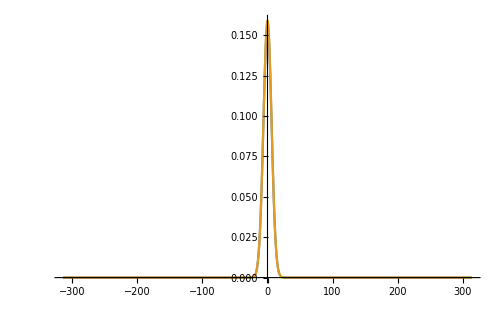

```mathematica
σ=1;
exact[x_,y_]:=(ⅇ^(-(x^2+y^2)/(2 σ^2)))/(2 π σ^2)
f[fx_,fy_]:=ⅇ^(-2 π^2 σ^2 (fx^2+ fy^2));
(*f[kx_,ky_]:=ⅇ^(-σ^2 (kx^2+ ky^2)/2);*)


(* Discretize from -Kmax to Kmax with the step delK over kx and ky *)
Kmax=2.;
delK=0.01;

KGrid=Join[-Reverse@#,Rest@#]&@Range[0.,Kmax,delK];
n=Length@KGrid;
(* Generate Reciprocal Grid *)
m=(n-1)/2;
delX = π/(delK m);
Xmax = m delX;
XGrid=delX Range[0.-m,m];

fF=delK^2 RotateRight[#,{m,m}]&@Fourier[#,FourierParameters->{1,1}]&@ RotateLeft[# ,{m,m}]&@ Outer[#,KGrid,KGrid] &@ f;

approx=ListInterpolation[fF,{XGrid,XGrid}];

Plot3D[Re@approx[x,y],{x,-Xmax,Xmax},{y,-Xmax,Xmax},PlotPoints->500,MaxRecursion->3,PlotRange->All,AxesLabel->{x,y}, PlotLabel->"Approx"]


Plot3D[Re@exact[x/(2 π),y/(2 π)],{x,-Xmax,Xmax},{y,-Xmax,Xmax},PlotPoints->500,MaxRecursion->3,PlotRange->All,Exclusions->None,AxesLabel->{x,y}, PlotLabel->"Exact"]

Plot[{Re@approx[x,1],Re@exact[x/(2 π),0]},{x,-Xmax,Xmax},Exclusions->None,PlotRange->All,ImageSize->500]

(*
Plot[{Im@approx[kx,1],Im@exact[kx,1]},{kx,-Kmax,Kmax},Exclusions->None,PlotRange->All,ImageSize->500]
*)
```

-Graphics3D-

Piecewise[{{1/50 (21+25 Cos[2 π x]+4 Cos[4 π x]), -1/2≤x≤1/2}, {0, True}}]

-Graphics3D-

-Graphics3D-

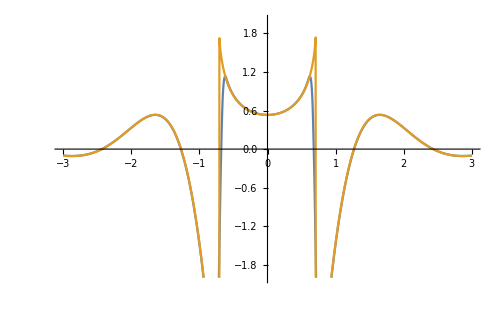

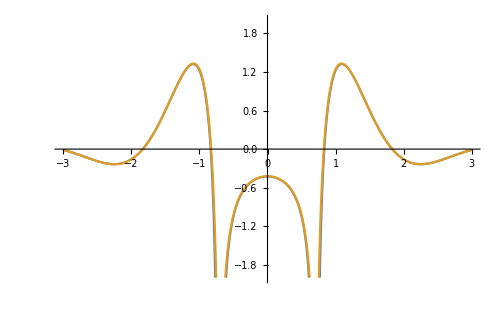

```mathematica
(*https://mathematica.stackexchange.com/questions/60973/2-dimensional-nfouriertransform*)
a=-2;
b=5 I-5;
f[x_,y_]:=1/(x^2+a y^2+b);

Plot3D[Re[f[x,y]],{x,-20,20},{y,-20,20},PlotPoints->200,MaxRecursion->5,PlotRange->All,AxesLabel->{x,y}]

(* Discretize from -R to R with the step d over x and y *)
R=100.;
delx=0.1;

xGrid=Join[-Reverse@#,Rest@#]&@Range[0.,R,delx];
n=Length@xGrid;
(* Generate Reciprocal Grid *)
m=(n-1)/2;
delk = π/(delx m);
kGrid=delk Range[0.-m,m];
X=ConstantArray[xGrid,n];
Y=Transpose@X;


F=f[X,Y];



(*F=Outer[f,xGrid,xGrid];*)

(*
W=# Transpose@#&@ConstantArray[BlackmanWindow[xGrid/R/2],n];
*)

FunctionExpand[BlackmanWindow[x]]

W=Outer[Times, BlackmanWindow[xGrid/R/2],BlackmanWindow[xGrid/R/2]];

(* Need a transpose at end compared to the naive Outer[f,xGrid,xGrid] implementation *)
fF=delx^2 Transpose @ RotateRight[#,{m,m}]&@Fourier[#,FourierParameters->{1,1}]&@ RotateLeft[F W,{m,m}];


(*fF=delx^2 RotateRight[#,{m,m}]&@Fourier[#,FourierParameters->{1,1}]&@RotateLeft[F W,{m,m}];*)

res=ListInterpolation[fF,{kGrid,kGrid}];

Plot3D[Im@res[kx,ky],{kx,-5,5},{ky,-5,5},PlotPoints->50,MaxRecursion->3,PlotRange->{-2,2},AxesLabel->{kx,ky}]

exact[kx_,ky_]:=2 π BesselK[0,Sqrt[b (kx^2+ky^2/a)]]/Sqrt[a]

Plot3D[Im@exact[kx,ky],{kx,-5,5},{ky,-5,5},PlotPoints->50,MaxRecursion->3,PlotRange->{-2,2},Exclusions->None,AxesLabel->{kx,ky}]

Plot[{Re@res[kx,1],Re@exact[kx,1]},{kx,-3,3},Exclusions->None,PlotRange->2,ImageSize->500]

Plot[{Im@res[kx,1],Im@exact[kx,1]},{kx,-3,3},Exclusions->None,PlotRange->2,ImageSize->500]
```

# Spherical Harmonics

```mathematica
SuperStar[z_]:=z/.Complex[a_,b_]:>Complex[a,-b]

Table[{l,m,Simplify[√(((2 l+1) (l-m)!)/((4 π) (l+m)!)) Subscript[P, l]^m(cos(θ)) ⅇ^(ⅈ m ϕ)==Subscript[Y, l]^m(θ,ϕ),0<θ<π]},{l,0,3},{m,-l,l}]
⟨{l_,m_},{L_,M_}⟩:=⟨{l,m},{L,M}⟩=⟨{L,M},{l,m}⟩=∫_0^(2 π) ∫_0^π SuperStar[Subscript[Y, l]^m(θ,ϕ)] Subscript[Y, L]^M(θ,ϕ) sin(θ)ⅆθⅆϕ
n=2;
Table[{{Subscript[l, 1],Subscript[m, 1]},{Subscript[l, 2],Subscript[m, 2]},⟨{Subscript[l, 1],Subscript[m, 1]},{Subscript[l, 2],Subscript[m, 2]}⟩==Subscript[δ, Subscript[l, 1],Subscript[l, 2]] Subscript[δ, Subscript[m, 1],Subscript[m, 2]]},{Subscript[l, 1],0,n},{Subscript[m, 1],-Subscript[l, 1],Subscript[l, 1]},{Subscript[l, 2],0,n},{Subscript[m, 2],-Subscript[l, 2],Subscript[l, 2]}]
```

{{{0,0,True}},{{1,-1,True},{1,0,True},{1,1,True}},{{2,-2,True},{2,-1,True},{2,0,True},{2,1,True},{2,2,True}},{{3,-3,True},{3,-2,True},{3,-1,True},{3,0,True},{3,1,True},{3,2,True},{3,3,True}}}

{{{{{{0,0},{0,0},True}},{{{0,0},{1,-1},True},{{0,0},{1,0},True},{{0,0},{1,1},True}},{{{0,0},{2,-2},True},{{0,0},{2,-1},True},{{0,0},{2,0},True},{{0,0},{2,1},True},{{0,0},{2,2},True}}}},{{{{{1,-1},{0,0},True}},{{{1,-1},{1,-1},True},{{1,-1},{1,0},True},{{1,-1},{1,1},True}},{{{1,-1},{2,-2},True},{{1,-1},{2,-1},True},{{1,-1},{2,0},True},{{1,-1},{2,1},True},{{1,-1},{2,2},True}}},{{{{1,0},{0,0},True}},{{{1,0},{1,-1},True},{{1,0},{1,0},True},{{1,0},{1,1},True}},{{{1,0},{2,-2},True},{{1,0},{2,-1},True},{{1,0},{2,0},True},{{1,0},{2,1},True},{{1,0},{2,2},True}}},{{{{1,1},{0,0},True}},{{{1,1},{1,-1},True},{{1,1},{1,0},True},{{1,1},{1,1},True}},{{{1,1},{2,-2},True},{{1,1},{2,-1},True},{{1,1},{2,0},True},{{1,1},{2,1},True},{{1,1},{2,2},True}}}},{{{{{2,-2},{0,0},True}},{{{2,-2},{1,-1},True},{{2,-2},{1,0},True},{{2,-2},{1,1},True}},{{{2,-2},{2,-2},True},{{2,-2},{2,-1},True},{{2,-2},{2,0},True},{{2,-2},{2,1},True},{{2,-2},{2,2},True}}},{{{{2,-1},{0,0},True}},{{{2,-1},{1,-1},True},{{2,-1},{1,0},True},{{2,-1},{1,1},True}},{{{2,-1},{2,-2},True},{{2,-1},{2,-1},True},{{2,-1},{2,0},True},{{2,-1},{2,1},True},{{2,-1},{2,2},True}}},{{{{2,0},{0,0},True}},{{{2,0},{1,-1},True},{{2,0},{1,0},True},{{2,0},{1,1},True}},{{{2,0},{2,-2},True},{{2,0},{2,-1},True},{{2,0},{2,0},True},{{2,0},{2,1},True},{{2,0},{2,2},True}}},{{{{2,1},{0,0},True}},{{{2,1},{1,-1},True},{{2,1},{1,0},True},{{2,1},{1,1},True}},{{{2,1},{2,-2},True},{{2,1},{2,-1},True},{{2,1},{2,0},True},{{2,1},{2,1},True},{{2,1},{2,2},True}}},{{{{2,2},{0,0},True}},{{{2,2},{1,-1},True},{{2,2},{1,0},True},{{2,2},{1,1},True}},{{{2,2},{2,-2},True},{{2,2},{2,-1},True},{{2,2},{2,0},True},{{2,2},{2,1},True},{{2,2},{2,2},True}}}}}

```mathematica
Image[{
{{1,0,0},{0,1,0},{0,0,1}},
{{0,0,1},{0,1,0},{1,0,0}}
},ColorSpace->"RGB"]
```

-Graphics-

# Fourier Basics!

```mathematica
(*https://mathematica.stackexchange.com/questions/85139/what-do-the-x-and-y-axis-stand-for-in-the-fourier-transform-domain/85167#85167*)
```

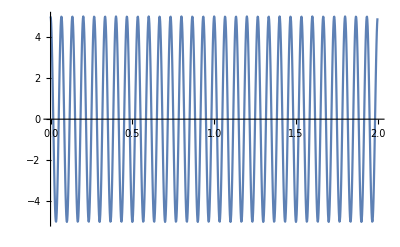

```mathematica
nn=1000;(*Number of points*)
sr=500;(*Sample rate Hz*)
dt=1/sr;(*Time increment seconds*)
df=sr/nn;(*Frequency increment*)
T = dt nn; (*period*)
df=1/T;(* or Frequency increment*)
f1=30/T;(*Example frequency at 15 Hz with exactly 30 periods in time interval*)
p=1/f1;(*Period of example frequency*)
a=5;(*Amplitude of cosine wave*)
data=Table[N[{t,a Cos[2 π f1 t]}],{t,0,dt (nn-1),dt}];
ListLinePlot[data]
```

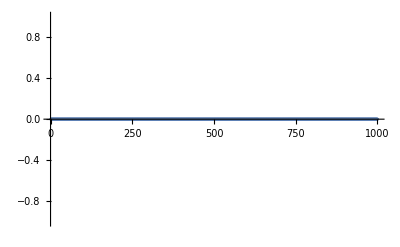

```mathematica
ft=Fourier[data[[All,2]],FourierParameters->{-1,-1}];
ListPlot[Re[ft],PlotRange->All]
```

```mathematica
FourierTransform[Sqrt[2/Pi] BesselK[0,u Sqrt[y^2+z^2] Sign[u]],{y},{t},Assumptions->{z∈Reals}]
```

FourierTransform[√(2/π) BesselK[0,u √(y^2+z^2) Sign[u]],{y},{t},Assumptions→{z∈ℝ}]

```mathematica
Fo[{u_,v_},{j_,k_},N_]:=ⅇ^(ⅈ (2 π)/N(u j + v k))
Fo[{0,0},{0,0}, 2^3]
```

1

```mathematica
(*https://mathematica.stackexchange.com/questions/179093/implementation-of-discrete-fourier-transform-in-matrix-form*)
```

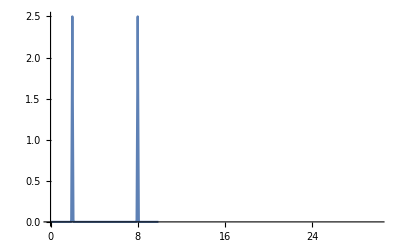

```mathematica
nn=100;(*number of points*)
sr=10;(*sample rate*)
dt=1/sr;(*time increment*)
df=sr/nn;(*frequency Increment*)
f1=2;
p=1/f1;
a=5;
data=Table[N[{t,a Cos[2 Pi f1 t]}],{t,0,dt (nn-1),dt}];
ft=Fourier[data[[All,2]],FourierParameters->{-1,-1}];
freqs=Table[(n-1) sr/nn,{n,nn}];
ListPlot[Transpose[{freqs,Abs[ft]}],PlotRange->{{0,30},All},Joined->True]
```

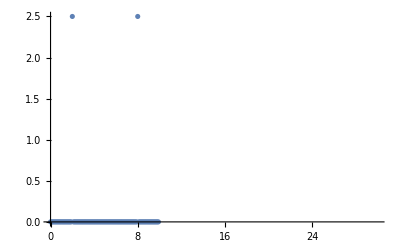

```mathematica
w=Table[N@Exp[(-I 2 Pi j k)/nn],{j,0,(nn-1)},{k,0,(nn-1)}]/Sqrt[nn];
discretefourier=Transpose[{freqs,Abs[dt (w.data[[All,2]])]}];
ListPlot[discretefourier,PlotRange->{{0,30},All}]
```

```mathematica
data[[All,2]]
```

{5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508}

```mathematica
Table[N[a Cos[2 Pi f1 t]],{t,0,dt (nn-1),dt}]
```

{5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508,5.,1.54508,-4.04508,-4.04508,1.54508}

```mathematica
data[[All,1]]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9}

```mathematica
??FourierMatrix
```

```mathematica
??*List*
```

```mathematica
ArrayReshape[Range[16],{4,4}]//MatrixForm
```

(1 | 2 | 3 | 4
5 | 6 | 7 | 8
9 | 10 | 11 | 12
13 | 14 | 15 | 16)

```mathematica
ArrayFlatten[#] &@{{ConstantArray[1,{2,2}],ConstantArray[2,{2,2}]},{ConstantArray[3,{2,2}],ConstantArray[4,{2,2}]}}//MatrixForm
```

(1 | 1 | 2 | 2
1 | 1 | 2 | 2
3 | 3 | 4 | 4
3 | 3 | 4 | 4)

```mathematica
RotateLeft[#, {2,2}] &@ArrayFlatten[#] &@{{ConstantArray[1,{2,2}],ConstantArray[2,{2,2}]},{ConstantArray[3,{2,2}],ConstantArray[4,{2,2}]}}//MatrixForm
```

(4 | 4 | 3 | 3
4 | 4 | 3 | 3
2 | 2 | 1 | 1
2 | 2 | 1 | 1)

```mathematica
??Flatten
```

```mathematica
{{ConstantArray[1,{2,2}],ConstantArray[2,{2,2}]},{ConstantArray[3,{2,2}],ConstantArray[4,{2,2}]}}//MatrixForm
```

```mathematica
Outer[List, {0,1,-2,-1}, {0,1,-2,-1}]//MatrixForm
```

((0
0) | (0
1) | (0
-2) | (0
-1)
(1
0) | (1
1) | (1
-2) | (1
-1)
(-2
0) | (-2
1) | (-2
-2) | (-2
-1)
(-1
0) | (-1
1) | (-1
-2) | (-1
-1))

```mathematica
K=10+ ⅈ/10//N;
x=0; y=0; z=3;

r=Sqrt[x^2+y^2+z^2];

kMax = 8;

nn=2^12;

dk=2 kMax/nn;

kgrid=Range[-kMax,kMax, dk];

kz[kx_,ky_]:=Module[{KSq=K^2, krSq = kx kx + ky ky},If[Re[KSq-krSq]≥0,√(KSq-krSq),ⅈ √(krSq-KSq)]];

g[kx_,ky_]:=Module[{gamma = kz[kx,ky]},ⅇ^(ⅈ gamma Abs[z])/(K gamma)]
G[kx_,ky_]:=dk^2/(2 π) g[kx,ky] ⅇ^(ⅈ (kx x + ky y))
Print["exact1: ", ⅇ^(ⅈ K r)/(ⅈ K r)]
Print["exact2: ", SphericalHankelH1[0, K r]]
Print["approx1: ",1/(2 π)NIntegrate[g[kx,ky] ⅇ^(ⅈ (kx x + ky y)),{kx,-kMax,kMax},{ky,-kMax,kMax}]]
Print["approx2: ",Total[Total[Outer[ G,kgrid,kgrid]]]]

(*SphericalHankelH1[0,k r]-ⅇ^(ⅈ k r)/(ⅈ k r)//Chop*)
```

exact1: -0.024434-0.00356474 ⅈ

exact2: -0.024434-0.00356474 ⅈ

approx1: -0.018754-0.00359221 ⅈ

approx2: -0.0187582-0.00363655 ⅈ

```mathematica
g[8, 8]
```

1.32639×10^-9-1.97192×10^-9 ⅈ

```mathematica
Subscript[T, 0]=r^3({{-(ⅈ (3 Δλ+2 Δμ) ω^3)/(3 (3 Δλ+2 Δμ+3 λ+6 μ) α^3), 0}, {0, 0}});

Subscript[T, 1]=r^3({{(ⅈ Δρ ω^3)/(9 ρ α^3), (ⅈ √2 Δρ  ω^3)/(9 ρ √(α^3 β^3))}, {(ⅈ √2 Δρ  ω^3)/(9 ρ √(α^3 β^3)), (2 ⅈ Δρ  ω^3)/(9 ρ β^3)}});
Subscript[T, 2]=r^3({{-(4 ⅈ Δμ μ ω^3)/(3 α^3 (15 μ (λ+2 μ)+Δμ (6 λ+16 μ))), -(2 ⅈ √(2/3) Δμ ρ ω^3)/(√(α β) (15 μ (λ+2 μ)+Δμ (6 λ+16 μ)))}, {-(2 ⅈ √(2/3) Δμ ρ ω^3)/(√(α β) (15 μ (λ+2 μ)+Δμ (6 λ+16 μ))), -(2 ⅈ Δμ (λ+2 μ) ω^3)/(β^3 (15 μ (λ+2 μ)+Δμ (6 λ+16 μ)))}});

Limit[Limit[Subscript[T, 0][[1,1]],Δμ->0],μ->0]/.α->ω/k//FullSimplify
Limit[Limit[Subscript[T, 1][[1,1]],Δμ->0],μ->0]/.α->ω/k//FullSimplify
Limit[Limit[Subscript[T, 2][[1,1]],Δμ->0],μ->0]/.α->ω/k//FullSimplify
```

-(ⅈ k^3 r^3 Δλ)/(3 (Δλ+λ))

(ⅈ k^3 r^3 Δρ)/(9 ρ)

0

```mathematica
j[n_Integer,r_]:=2^n r^n ∑_(s=0)^2 ((-1)^s(s+n)!)/(s! (2s+2n+1)!)r^(2s);
h[n_Integer,z_]:=(-ⅈ)^(n+1) (1+ⅈ z-z^2/2-(ⅈ z^3)/6+z^4/24)/z ∑_(s=0)^n ((ⅈ)^s(n+s)!)/(s! (2z)^s(n-s)!);
J=({{0, 1}, {-1, 0}});

α1=Sqrt[λ1/ρ1];
α2=Sqrt[λ2/ρ2];
K1=ω/α1;
K2=ω/α2;

Bre1[n_, r_]:=({{j[n, K1 r]}, {D[j[n, K1 r],r]/ρ1}});
Bou1[n_,r_]:=({{h[n, K1 r]}, {D[h[n, K1 r],r]/ρ1}});
Bre2[n_,r_]:=({{j[n, K2 r]}, {D[j[n, K2 r],r]/ρ2}});

(*Series[r^2 Transpose[Bre1[0,r]].J.Bou1[0,r],{r,0,3},Assumptions->{r ∈ Reals}]//Normal//FullSimplify
Series[r^2 Transpose[Bre1[0,r]].J.Bre2[0,r],{r,0,3},Assumptions->{r ∈ Reals}]//Normal//FullSimplify

Series[r^2 Transpose[Bre1[1,r]].J.Bou1[1,r],{r,0,3},Assumptions->{r ∈ Reals}]//Normal//FullSimplify
Series[r^2 Transpose[Bre1[1,r]].J.Bre2[1,r],{r,0,3},Assumptions->{r ∈ Reals}]//Normal//FullSimplify*)

n=0;
t0=Series[(Transpose[Bre1[n,r]].J.Bre2[n,r])/(Transpose[Bre1[n,r]].J.Bou1[n,r]),{r,0,3},Assumptions->{r ∈ Reals}][[1,1]]//Normal//PowerExpand//FullSimplify
n=1;
t1=Series[(Transpose[Bre1[n,r]].J.Bre2[n,r])/(Transpose[Bre1[n,r]].J.Bou1[n,r]),{r,0,3},Assumptions->{r ∈ Reals}][[1,1]]//Normal//PowerExpand//FullSimplify
```

(ⅈ r^3 (λ1-λ2) ρ1^(3/2) ω^3)/(3 λ1^(3/2) λ2)

-(ⅈ r^3 ρ1 (ρ1-ρ2) ω^3)/(9 λ1 √λ2 √ρ2)

```mathematica
t0//.{λ1->ρ1 α1^2,λ2->ρ2 α2^2 }

t1//.{λ1->ρ1 α1^2,λ2->ρ2 α2^2 }
```

(ⅈ r^3 (λ1-λ2) ρ1^(3/2) ω^3)/(3 λ1^(3/2) λ2)

-(ⅈ r^3 ρ1 (ρ1-ρ2) ω^3)/(9 λ1 √λ2 √ρ2)

```mathematica
t0[[1,1]]
```

(ⅈ r^3 (λ1-λ2) ρ1^(3/2) ω^3)/(3 λ1^(3/2) λ2)